# CEPC Higgs Precision

(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliu2@fnal.gov) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

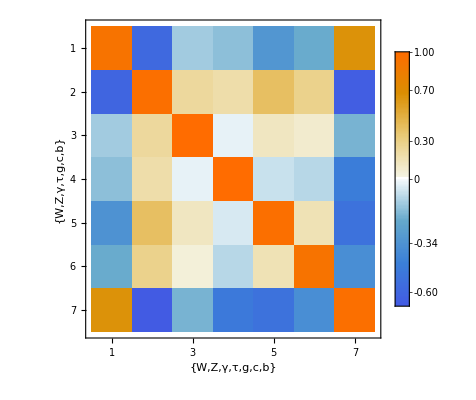

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

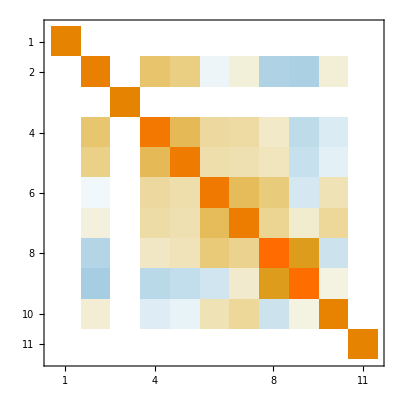

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0118029
-0.0117799)
(0.0211339
-0.0210743)
(0.0145802
-0.0144704)
(0.013066
-0.0130661)
(0.0133536
-0.0132739)
(0.00124944
-0.00125111)
(0.0361112
-0.0368686))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}}
kc | {{2.11,-2.11}}
kg | {{1.46,-1.45}}
kw | {{1.31,-1.31}}
ktau | {{1.34,-1.33}}
kz | {{0.12,-0.13}}
kgamma | {{3.61,-3.69}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(160322. | -6920.58 | -25106.6 | -54408.8 | -51941.2 | 136003. | -855.77
-6920.58 | 4057.33 | 2317.66 | 636.328 | -1205.34 | -10368.8 | 3.48455
-25106.6 | 2317.66 | 24988.2 | -788.767 | -4626.86 | -21278.4 | -16.8215
-54408.8 | 636.328 | -788.767 | 50529.1 | -670.021 | -83996.2 | 19.241
-51941.2 | -1205.34 | -4626.86 | -670.021 | 56092.4 | 20726. | -96.6801
136003. | -10368.8 | -21278.4 | -83996.2 | 20726. | 916713. | -1000.06
-855.77 | 3.48455 | -16.8215 | 19.241 | -96.6801 | -1000.06 | 855.506)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.0002 | 0.634277 | 0.891241 | 0.928746 | 0.947297 | -0.365763 | 0.345717
0.634277 | 0.999881 | 0.493384 | 0.590633 | 0.611401 | -0.138108 | 0.221453
0.891241 | 0.493384 | 1.00011 | 0.84096 | 0.858591 | -0.27462 | 0.312383
0.928746 | 0.590633 | 0.84096 | 1.0002 | 0.877789 | -0.203175 | 0.325402
0.947297 | 0.611401 | 0.858591 | 0.877789 | 1.00015 | -0.366908 | 0.33096
-0.365763 | -0.138108 | -0.27462 | -0.203175 | -0.366908 | 1. | -0.0934936
0.345717 | 0.221453 | 0.312383 | 0.325402 | 0.33096 | -0.0934936 | 0.998827)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.634252 | 0.891103 | 0.928563 | 0.947136 | -0.365727 | 0.345886
0.634252 | 1. | 0.493385 | 0.590609 | 0.611392 | -0.138116 | 0.221596
0.891103 | 0.493385 | 1. | 0.840829 | 0.85848 | -0.274604 | 0.312548
0.928563 | 0.590609 | 0.840829 | 1. | 0.877638 | -0.203155 | 0.32556
0.947136 | 0.611392 | 0.85848 | 0.877638 | 1. | -0.366881 | 0.33113
-0.365727 | -0.138116 | -0.274604 | -0.203155 | -0.366881 | 1. | -0.0935484
0.345886 | 0.221596 | 0.312548 | 0.32556 | 0.33113 | -0.0935484 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.2,1.2}} | {{0.9,0.9}}
kc | {{2.1,2.1}} | {{1.9,1.9}}
kg | {{1.5,1.4}} | {{1.1,1.1}}
kw | {{1.3,1.3}} | {{1.,1.}}
ktau | {{1.3,1.3}} | {{1.1,1.1}}
kz | {{0.1,0.1}} | {{0.1,0.1}}
kgamma | {{3.6,3.7}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.92,-0.92}}
kc | {{1.86,-1.86}}
kg | {{1.12,-1.11}}
kw | {{1.02,-1.02}}
ktau | {{1.06,-1.06}}
kz | {{0.12,-0.12}}
kgamma | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{163850.,-6765.56,-30395.9,-53159.4,-51571.5,130191.,-842.466},{-6765.56,4464.51,1672.6,694.216,-1188.21,-10629.7,4.10095},{-30395.9,1672.6,34243.3,-2763.87,-5211.36,-12872.4,-37.8527},{-53159.4,694.216,-2763.87,53263.2,-531.952,-88366.1,24.209},{-51571.5,-1188.21,-5211.36,-531.952,56566.4,19670.8,-95.21},{130191.,-10629.7,-12872.4,-88366.1,19670.8,932650.,-4108.87},{-842.466,4.10095,-37.8527,24.209,-95.21,-4108.87,3941.98}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00007 | 0.568505 | 0.869307 | 0.884889 | 0.916009 | -0.305686 | 0.11436
0.568505 | 0.99986 | 0.446228 | 0.506599 | 0.536605 | -0.0609252 | 0.0729729
0.869307 | 0.446228 | 1.00004 | 0.791765 | 0.816929 | -0.228556 | 0.104253
0.884889 | 0.506599 | 0.791765 | 1.00007 | 0.807764 | -0.0926284 | 0.114409
0.916009 | 0.536605 | 0.816929 | 0.807764 | 1.00004 | -0.306455 | 0.105363
-0.305686 | -0.0609252 | -0.228556 | -0.0926284 | -0.306455 | 1. | 0.0352107
0.11436 | 0.0729729 | 0.104253 | 0.114409 | 0.105363 | 0.0352107 | 0.999981)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.568526 | 0.86926 | 0.884826 | 0.915959 | -0.305676 | 0.114357
0.568526 | 1. | 0.44625 | 0.506615 | 0.536632 | -0.0609295 | 0.0729788
0.86926 | 0.44625 | 1. | 0.791719 | 0.816895 | -0.228551 | 0.104252
0.884826 | 0.506615 | 0.791719 | 1. | 0.807718 | -0.0926249 | 0.114405
0.915959 | 0.536632 | 0.816895 | 0.807718 | 1. | -0.306449 | 0.105362
-0.305676 | -0.0609295 | -0.228551 | -0.0926249 | -0.306449 | 1. | 0.035211
0.114357 | 0.0729788 | 0.104252 | 0.114405 | 0.105362 | 0.035211 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0129954
-0.0129244)
(0.0216494
-0.0215376)
(0.0155011
-0.0153488)
(0.0138088
-0.0137778)
(0.0145525
-0.0144235)
(0.00249677
-0.0025029)
(0.0364716
-0.0371533)
(0.0834764
-0.0903147)
(0.00150002
-0.00150001)
(0.0287935
-0.0281479))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.03}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651845 | 0.90324 | 0.933432 | 0.955589 | 0.192915 | 0.366548 | 0.155284 | 0. | 0.981764
0.651845 | 0.999876 | 0.525309 | 0.614638 | 0.632549 | 0.115783 | 0.242468 | 0.102719 | 0. | 0.64735
0.90324 | 0.525309 | 1.0001 | 0.857997 | 0.87563 | 0.162086 | 0.335992 | 0.142339 | 0. | 0.897333
0.933432 | 0.614638 | 0.857997 | 1.0002 | 0.89039 | 0.181259 | 0.347828 | 0.147354 | 0. | 0.931309
0.955589 | 0.632549 | 0.87563 | 0.89039 | 1.00012 | 0.172568 | 0.353482 | 0.149749 | 0. | 0.944404
0.192915 | 0.115783 | 0.162086 | 0.181259 | 0.172568 | 1.00013 | 0.0679164 | 0.0287721 | 0. | 0.351261
0.366548 | 0.242468 | 0.335992 | 0.347828 | 0.353482 | 0.0679164 | 0.998814 | 0.0574918 | 0. | 0.362868
0.155284 | 0.102719 | 0.142339 | 0.147354 | 0.149749 | 0.0287721 | 0.0574918 | 0.992493 | 0. | 0.153725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999976 | 0.
0.981764 | 0.64735 | 0.897333 | 0.931309 | 0.944404 | 0.351261 | 0.362868 | 0.153725 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0103186
-0.0102576)
(0.0190288
-0.0189831)
(0.0120981
-0.0119974)
(0.0108282
-0.0107985)
(0.0117734
-0.0116744)
(0.00249688
-0.00250313)
(0.0162701
-0.0162915)
(0.0494669
-0.0502318)
(0.00150001
-0.00150002)
(0.0233043
-0.0228486))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{1.03,-1.03}}
kt | {{2.16,-2.15}} | {{1.9,-1.9}}
kg | {{1.55,-1.53}} | {{1.21,-1.2}}
kw | {{1.38,-1.38}} | {{1.08,-1.08}}
ktau | {{1.46,-1.44}} | {{1.18,-1.17}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}} | {{1.63,-1.63}}
kmu | {{8.35,-9.03}} | {{4.95,-5.02}}
brinv | {{0.15,-0.15}} | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}} | {{2.33,-2.28}})

```mathematica
-Graphics-;
```

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 1.
kt | 2.2 | 1.9
kg | 1.5 | 1.2
kw | 1.4 | 1.1
ktau | 1.4 | 1.2
kz | 0.2 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 2.8 | 2.3)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00004 | 0.587306 | 0.888449 | 0.89504 | 0.931422 | 0.242999 | 0.170569 | 0.079863 | 0. | 0.972108
0.587306 | 0.999853 | 0.480479 | 0.534928 | 0.561192 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.888449 | 0.480479 | 1.00002 | 0.817183 | 0.844922 | 0.207507 | 0.153268 | 0.072064 | 0. | 0.879634
0.89504 | 0.534928 | 0.817183 | 1.00007 | 0.831244 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931422 | 0.561192 | 0.844922 | 0.831244 | 1.00002 | 0.213239 | 0.159251 | 0.0749429 | 0. | 0.915309
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.050151 | 0. | 0.43334
0.170569 | 0.100895 | 0.153268 | 0.157685 | 0.159251 | 0.153555 | 0.999969 | 0.0174489 | 0. | 0.191394
0.079863 | 0.0475803 | 0.072064 | 0.0736481 | 0.0749429 | 0.050151 | 0.0174489 | 0.999778 | 0. | 0.0851411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999979 | 0.
0.972108 | 0.581922 | 0.879634 | 0.894973 | 0.915309 | 0.43334 | 0.191394 | 0.0851411 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999926,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.99999,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

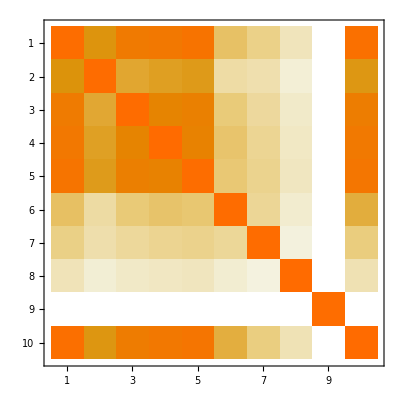

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## CDR (width subchannel ZZ)

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,0,0.1,0.002}]
```

{{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483}}

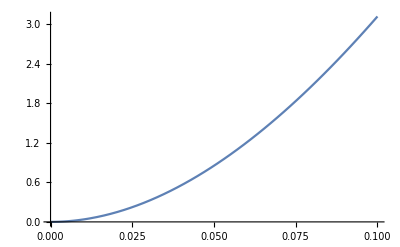

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,0,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

## CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1111.78 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2-10478.4 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+106240. (-1+(kb^2 kz^2)/ktotal)^2-31.8463 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+645.239 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10412.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.0851},{-0.098,7.76173},{-0.096,7.44509},{-0.094,7.13516},{-0.092,6.83194},{-0.09,6.53541},{-0.088,6.24558},{-0.086,5.96243},{-0.084,5.68595},{-0.082,5.41615},{-0.08,5.153},{-0.078,4.89652},{-0.076,4.64667},{-0.074,4.40347},{-0.072,4.16689},{-0.07,3.93694},{-0.068,3.71361},{-0.066,3.49689},{-0.064,3.28676},{-0.062,3.08323},{-0.06,2.88628},{-0.058,2.69591},{-0.056,2.51211},{-0.054,2.33487},{-0.052,2.16419},{-0.05,2.00004},{-0.048,1.84244},{-0.046,1.69137},{-0.044,1.54682},{-0.042,1.40878},{-0.04,1.27724},{-0.038,1.15221},{-0.036,1.03366},{-0.034,0.921593},{-0.032,0.816},{-0.03,0.716871},{-0.028,0.624198},{-0.026,0.537973},{-0.024,0.458188},{-0.022,0.384834},{-0.02,0.317903},{-0.018,0.257386},{-0.016,0.203276},{-0.014,0.155563},{-0.012,0.11424},{-0.01,0.0792977},{-0.008,0.0507277},{-0.006,0.0285214},{-0.004,0.0126705},{-0.002,0.00316618},{0.,1.63667×10^-21},{0.002,0.00316331},{0.004,0.0126475},{0.006,0.0284438},{0.008,0.0505437},{0.01,0.0789384},{0.012,0.113619},{0.014,0.154577},{0.016,0.201804},{0.018,0.25529},{0.02,0.315028},{0.022,0.381008},{0.024,0.453221},{0.026,0.531658},{0.028,0.616311},{0.03,0.707171},{0.032,0.804228},{0.034,0.907474},{0.036,1.0169},{0.038,1.1325},{0.04,1.25426},{0.042,1.38217},{0.044,1.51622},{0.046,1.65641},{0.048,1.80273},{0.05,1.95516},{0.052,2.1137},{0.054,2.27834},{0.056,2.44907},{0.058,2.62588},{0.06,2.80876},{0.062,2.9977},{0.064,3.19269},{0.066,3.39373},{0.068,3.6008},{0.07,3.81389},{0.072,4.03301},{0.074,4.25812},{0.076,4.48924},{0.078,4.72634},{0.08,4.96942},{0.082,5.21848},{0.084,5.47349},{0.086,5.73445},{0.088,6.00135},{0.09,6.27418},{0.092,6.55294},{0.094,6.83761},{0.096,7.12818},{0.098,7.42465},{0.1,7.72701}}

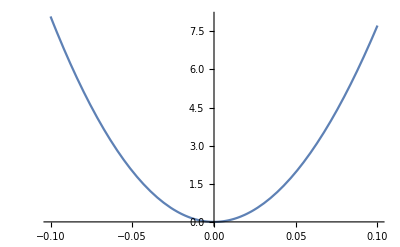

{{x→0.0356983}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.1,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

# MuC Higgs Precision

(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliuphy@umn.edu) for detailed explanation.

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## Inputs

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
brzgamma=1.533*10^-3;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kw_,kz_,kg_,kgamma_,kza_,kc_,kt_,kb_,kmu_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kc^2 brc+kb^2 brs+kmu^2 brmu+kza^2 brzgamma+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu-brzgamma);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1,1,1]
```

kh[1,1,1,1,1,1,1,1,1]

### CEPC CDR inputs dated: July.2.2018 by Zhen (based on inputs developed in May)

```mathematica
higgsobscepc[kw_,kz_,kg_,kgamma_,kza_,kc_,kt_,kb_,kmu_,ktau_]:={kz^2 kmu^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 ktau^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kgamma^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^4/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kg^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kc^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kw^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],6/7 kz^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau]+1/7 kw^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2,kw^2 kza^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau]};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2,8.2}/100;
higgsprecepc=(*July.20.2018; Note that the second to last entry is infinity to avoid double counting*){16.8,0.87,7.25,1.00,5.21,1.34,3.43,0.324,3.16,Infinity(*(0.00401209+0.00402172)*100/2*),0.5,8.2}/100;
higgsobscepcinv=0.165/100;
halfcorrelation=(*July.20.2018*)SparseArray[{{12,12}->0,{4,2}->-13.286,{5,2}->-6.669,{6,2}->0.864,{7,2}->0.638,{8,2}->-0.025,{9,2}->-0.011,{10,2}->-0.075,{5,4}->-32.350,{6,4}->-3.644,{7,4}->-2.869,{8,4}->1.140,{9,4}->-0.521,{10,4}->0.328,{6,5}->-1.926,{7,5}->-1.167,{8,5}->-1.809,{9,5}->0.827,{10,5}->0.148,{7,6}->-22.332,{8,6}->-12.429,{9,6}-> 5.681,{10,6}->-1.680,{8,7}-> -7.027,{9,7}-> 3.212,{10,7}-> -6.498,{9,8}-> -45.706,{10,8}-> 0.918,{10,9}-> -0.420}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[12]*100+halfcorrelationᵀ+halfcorrelation;
MatrixPlot[Abs[inputcorrelations],FrameLabel->{{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"},{"Zμ","Zτ","Zγ","ZW","ZZ","Zg","Zc","Zb","WWbb","vvb","ZH"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelations[[i,j]],3],{i-0.5,12-j+0.5}],{i,1,12},{j,1,12}]]]
```

-Graphics-

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0. | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0. | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0. | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0. | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0. | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0. | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
Length[inputcorrelations]
```

12

### HL-LHC ECFA updated inputs

For constrained kappa for now

From https://twiki.cern.ch/twiki/bin/view/LHCPhysics/GuidelinesCouplingProjections2018

```mathematica
higgsobslhc7s2[kw_,kz_,kg_,kgamma_,kza_,kc_,kt_,kb_,kmu_,ktau_]:={kgamma,kw,kz,kg,kt,kb,ktau,kmu};
higgsprelhc7s2={2.0,1.8,1.7,2.5,3.5,4.0,2.0,5.0}/100;
halfcorrelationlhc7s2=(*July.20.2018*)SparseArray[{{1,2}->0.66,{1,3}->0.57,{1,4}->0.29,{1,5}->0.18,{1,6}->0.65,{1,7}->0.66,{1,8}->0.27,
{2,3}->0.58,{2,4}->0.39,{2,5}->0.25,{2,6}->0.74,{2,7}->0.59,{2,8}->0.27,
{3,4}->0.24,{3,5}->0.24,{3,6}->0.56,{3,7}->0.50,{3,8}->0.23,
{4,5}->0.34,{4,6}->0.67,{4,7}->0.43,{4,8}->0.09,
{5,6}->0.38,{5,7}->0.26,{5,8}->0.09,
{6,7}->0.70,{6,8}->0.26,
{7,8}->0.25,{8,8}->0}]//Normal;
inputcorrelationslhc7s2=(*Apr.15.2018*)IdentityMatrix[8]*100+halfcorrelationlhc7s2ᵀ*100+halfcorrelationlhc7s2*100;
MatrixPlot[Abs[inputcorrelationslhc7s2],FrameLabel->{{"κγ","κw","κz","κg","κt","κb","κτ","κμ"}},PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelationslhc7s2[[i,j]],3],{i-0.5,Length[inputcorrelationslhc7s2]-j+0.5}],{i,1,Length[inputcorrelationslhc7s2]},{j,1,Length[inputcorrelationslhc7s2]}]]]
```

-Graphics-

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0. | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0. | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0. | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0. | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0. | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0. | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

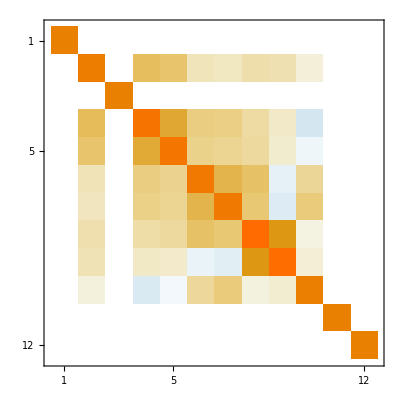

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0. | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0. | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0. | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0. | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0. | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0. | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0 | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0 | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0 | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

Part::partw: Part 8 of higgsobscepc[kz,kw,kg,kgamma,1.01479,kt,ktau] does not exist.

Part::partw: Part 8 of higgsobscepc[kz,kw,kg,kgamma,kb,1.00619,ktau] does not exist.

Part::partw: Part 8 of higgsobscepc[kz,kw,1.02119,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 8 of higgsobscepc[kz,1.0105,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,kg,kgamma,1.01479,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,kg,kgamma,kb,1.00619,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,1.02119,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,1.0105,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,kg,kgamma,1.01479,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,kg,kgamma,kb,1.00619,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,1.02119,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,1.0105,kg,kgamma,kb,kt,ktau] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::nnum: The function value 3302.33+3185.04 (-1+higgsobscepc[«1»]⟦8⟧)+«19» «1»+«3»+40000. («1»)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 2134.41-170.413 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3687.42+3329.12 («1»)+122965. «1»+«3»+40000. (-1+«1»⟦11⟧)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3490.04+3325.5 (-1+higgsobscepc[«1»]⟦8⟧)+«19» «1»+«3»+40000. («1»)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3286.8+3177.92 (-1+higgsobscepc[«1»]⟦8⟧)+«19» «1»+«3»+40000. («1»)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 2139.5-505.44 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3687.37+3329.12 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3441.7+3324.08 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

Part::partw: Part 8 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,1.03384] does not exist.

Part::partw: Part 8 of higgsobscepc[1.01048,kw,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 8 of higgsobscepc[kz,kw,kg,1.00472,kb,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,1.03384] does not exist.

Part::partw: Part 9 of higgsobscepc[1.01048,kw,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,kg,1.00472,kb,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,1.03384] does not exist.

Part::partw: Part 10 of higgsobscepc[1.01048,kw,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,kg,1.00472,kb,kt,ktau] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::nnum: The function value 3864.34+3865.83 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3718.99+3329.12 («1»)+«4»+40000. (-1+«1»⟦11⟧)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 1777.19+3224.91 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3823.32+3752.69 (-1+higgsobscepc[«1»]⟦8⟧)+«19» «1»+«3»+40000. («1»)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 3719.+3329.12 («1»)+122965. «1»+«3»+40000. (-1+«1»⟦11⟧)^2+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

NMinimize::nnum: The function value 1755.42+3220.35 (-1+higgsobscepc[1.44707,«6»]⟦8⟧)+«4»+«7» «1»+148.721 (-1+higgsobscepc[«1»]⟦12⟧)^2 is not a number at {kb,kg,kgamma,kt,ktau,kw,kz} = {1.51398,1.45118,1.35209,1.50583,0.753875,1.08751,1.44707}.

```mathematica
cepc7p//MatrixForm
```

((0.0147918
-0.00986929)
(0.00618566
-0.0416472)
(0.0211919
-0.0122052)
(0.0105009
-0.0196425)
(0.0338371
-0.0251788)
(0.0104786
-0.0186418)
(0.00472209
-0.0104697))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{2.71,-2.96}}
kc | {{0.1,-3.98}}
kg | {{3.79,-0.01}}
kw | {{1.69,-4.81}}
ktau | {{0.48,-2.89}}
kz | {{0.21,-4.87}}
kgamma | {{1.34,-1.16}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

Part::partw: Part 8 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 9 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau] does not exist.

Part::partw: Part 10 of higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression System`Private`DerivativeX[2] cannot be used as a part specification.

(1)
 |  |  |  |

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

Part::partw: Part 8 of higgsobscepc[1.,1.,1.,1.,1.,1.,1.] does not exist.

Part::partw: Part 9 of higgsobscepc[1.,1.,1.,1.,1.,1.,1.] does not exist.

Part::partw: Part 8 of higgsobscepc[1.,1.,1.,1.,1.,1.,1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted[]

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

$Aborted

$Aborted

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.2,1.2}} | {{0.9,0.9}}
kc | {{2.1,2.1}} | {{1.9,1.9}}
kg | {{1.5,1.4}} | {{1.1,1.1}}
kw | {{1.3,1.3}} | {{1.,1.}}
ktau | {{1.3,1.3}} | {{1.1,1.1}}
kz | {{0.1,0.1}} | {{0.1,0.1}}
kgamma | {{3.6,3.7}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.92,-0.92}}
kc | {{1.86,-1.86}}
kg | {{1.12,-1.11}}
kw | {{1.02,-1.02}}
ktau | {{1.06,-1.06}}
kz | {{0.12,-0.12}}
kgamma | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{163850.,-6765.56,-30395.9,-53159.4,-51571.5,130191.,-842.466},{-6765.56,4464.51,1672.6,694.216,-1188.21,-10629.7,4.10095},{-30395.9,1672.6,34243.3,-2763.87,-5211.36,-12872.4,-37.8527},{-53159.4,694.216,-2763.87,53263.2,-531.952,-88366.1,24.209},{-51571.5,-1188.21,-5211.36,-531.952,56566.4,19670.8,-95.21},{130191.,-10629.7,-12872.4,-88366.1,19670.8,932650.,-4108.87},{-842.466,4.10095,-37.8527,24.209,-95.21,-4108.87,3941.98}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00007 | 0.568505 | 0.869305 | 0.884889 | 0.916009 | -0.305686 | 0.11436
0.568505 | 0.99986 | 0.446227 | 0.506599 | 0.536605 | -0.0609252 | 0.0729729
0.869305 | 0.446227 | 1.00004 | 0.791763 | 0.816927 | -0.228556 | 0.104253
0.884889 | 0.506599 | 0.791763 | 1.00007 | 0.807765 | -0.0926284 | 0.114409
0.916009 | 0.536605 | 0.816927 | 0.807765 | 1.00004 | -0.306455 | 0.105363
-0.305686 | -0.0609252 | -0.228556 | -0.0926284 | -0.306455 | 1. | 0.0352106
0.11436 | 0.0729729 | 0.104253 | 0.114409 | 0.105363 | 0.0352106 | 0.999979)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.568526 | 0.86926 | 0.884826 | 0.915959 | -0.305676 | 0.114357
0.568526 | 1. | 0.44625 | 0.506615 | 0.536632 | -0.0609295 | 0.0729788
0.86926 | 0.44625 | 1. | 0.791719 | 0.816895 | -0.228551 | 0.104252
0.884826 | 0.506615 | 0.791719 | 1. | 0.807718 | -0.0926249 | 0.114405
0.915959 | 0.536632 | 0.816895 | 0.807718 | 1. | -0.306449 | 0.105362
-0.305676 | -0.0609295 | -0.228551 | -0.0926249 | -0.306449 | 1. | 0.035211
0.114357 | 0.0729788 | 0.104252 | 0.114405 | 0.105362 | 0.035211 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0129954
-0.0129245)
(0.0216494
-0.0215375)
(0.0155011
-0.0153488)
(0.0138088
-0.0137778)
(0.0145524
-0.0144235)
(0.00249677
-0.00250291)
(0.0364714
-0.0371532)
(0.0834764
-0.0903149)
(0.00150002
-0.00150002)
(0.0287935
-0.0281479))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.03}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651846 | 0.90324 | 0.933432 | 0.955593 | 0.192915 | 0.366549 | 0.155284 | 0. | 0.981765
0.651846 | 0.999879 | 0.52531 | 0.614638 | 0.632552 | 0.115783 | 0.242469 | 0.102719 | 0. | 0.647351
0.90324 | 0.52531 | 1.0001 | 0.857996 | 0.875632 | 0.162086 | 0.335992 | 0.142339 | 0. | 0.897333
0.933432 | 0.614638 | 0.857996 | 1.0002 | 0.890391 | 0.181259 | 0.347829 | 0.147354 | 0. | 0.931309
0.955593 | 0.632552 | 0.875632 | 0.890391 | 1.00013 | 0.172568 | 0.353484 | 0.149749 | 0. | 0.944407
0.192915 | 0.115783 | 0.162086 | 0.181259 | 0.172568 | 1.00013 | 0.0679165 | 0.028772 | 0. | 0.351261
0.366549 | 0.242469 | 0.335992 | 0.347829 | 0.353484 | 0.0679165 | 0.998819 | 0.0574919 | 0. | 0.362869
0.155284 | 0.102719 | 0.142339 | 0.147354 | 0.149749 | 0.028772 | 0.0574919 | 0.992491 | 0. | 0.153725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999975 | 0.
0.981765 | 0.647351 | 0.897333 | 0.931309 | 0.944407 | 0.351261 | 0.362869 | 0.153725 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0103186
-0.0102576)
(0.0190289
-0.0189831)
(0.0120981
-0.0119974)
(0.0108282
-0.0107985)
(0.0117734
-0.0116744)
(0.00249688
-0.00250313)
(0.0162701
-0.0162915)
(0.0494669
-0.0502318)
(0.00150002
-0.00150001)
(0.0233043
-0.0228486))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{1.03,-1.03}}
kt | {{2.16,-2.15}} | {{1.9,-1.9}}
kg | {{1.55,-1.53}} | {{1.21,-1.2}}
kw | {{1.38,-1.38}} | {{1.08,-1.08}}
ktau | {{1.46,-1.44}} | {{1.18,-1.17}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}} | {{1.63,-1.63}}
kmu | {{8.35,-9.03}} | {{4.95,-5.02}}
brinv | {{0.15,-0.15}} | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}} | {{2.33,-2.28}})

```mathematica
-Graphics-;
```

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 1.
kt | 2.2 | 1.9
kg | 1.5 | 1.2
kw | 1.4 | 1.1
ktau | 1.4 | 1.2
kz | 0.2 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 2.8 | 2.3)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.0144879,0.00249984,0.0368123,0.0868956,0.00150002,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.0144879,0.00249984,0.0368123,0.0868956,0.00150002,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00005 | 0.587306 | 0.88845 | 0.895041 | 0.931422 | 0.242999 | 0.17057 | 0.0798631 | 0. | 0.972109
0.587306 | 0.999851 | 0.480479 | 0.534927 | 0.561191 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.88845 | 0.480479 | 1.00002 | 0.817183 | 0.844922 | 0.207507 | 0.153268 | 0.072064 | 0. | 0.879634
0.895041 | 0.534927 | 0.817183 | 1.00007 | 0.831243 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931422 | 0.561191 | 0.844922 | 0.831243 | 1.00002 | 0.213239 | 0.15925 | 0.0749428 | 0. | 0.915308
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.0501509 | 0. | 0.43334
0.17057 | 0.100895 | 0.153268 | 0.157685 | 0.15925 | 0.153555 | 0.99997 | 0.0174489 | 0. | 0.191394
0.0798631 | 0.0475803 | 0.072064 | 0.0736481 | 0.0749428 | 0.0501509 | 0.0174489 | 0.999777 | 0. | 0.0851411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.99998 | 0.
0.972109 | 0.581922 | 0.879634 | 0.894973 | 0.915308 | 0.43334 | 0.191394 | 0.0851411 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999926,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.99999,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

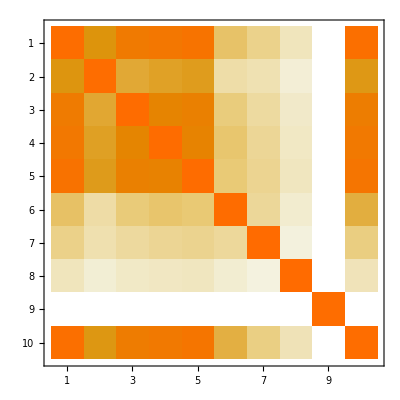

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## MuC (9 parameter fit; without Br_inv)

```mathematica
Clear[chisquaremuc10p]
```

```mathematica
higgsobsmuc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal};
chisquaremuc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)^2/higgspremuc[[i]]^2)/lumif,{i,1,Length[higgspremuc]}]
```

```mathematica
140/4200//N
```

0.0333333

```mathematica
higgspremuc={2000,17.75,374,1.62, 4.49,12.8,25.23,1.72,140/4200*100}/100.
```

{20.,0.1775,3.74,0.0162,0.0449,0.128,0.2523,0.0172,0.0333333}

```mathematica
func=chisquaremuc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal},1]
```

3380.21 (-1+(kb^2 kmu^2)/ktotal)^2+61.0352 (-1+(kg^2 kmu^2)/ktotal)^2+0.0714919 (-1+(kgamma^2 kmu^2)/ktotal)^2+0.0025 (-1+kmu^4/ktotal)^2+15.7096 (-1+(kmu^2 kt^2)/ktotal)^2+31.7397 (-1+(kmu^2 ktau^2)/ktotal)^2+900. (-1+ktotal)^2+3810.39 (-1+(kmu^2 kw^2)/ktotal)^2+496.029 (-1+(kmu^2 kz^2)/ktotal)^2

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1}}],Method->"FinestGrained"];
muc10p//MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {0.807031,0.183332,0.536169,1.44098,0.704476,0.,0.,0.217763,0.123374}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

((ComplexInfinity
-1.49397)
(1.23803
-0.543961)
(ComplexInfinity
-0.522083)
(ComplexInfinity
ComplexInfinity)
(1.17
-0.530298)
(ComplexInfinity
-1.491)
(3.35149
-5.3471)
(1.14219
-0.508837)
(0.0333333
-0.0333333))

```mathematica
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
```

```mathematica
inverseinputcorrelationslhc7s2=Inverse[inputcorrelationslhc7s2/100];
chisquaremuc10pLHC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10pLHC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc10pLHC//MatrixForm
```

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(1.04667 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(1.06504 kmu^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,((«3»)^2 «1»)/ktotal,(«19» kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(1.04485 «1»)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(1.04667 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(1.06504 kmu^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,((«3»)^2 «1»)/ktotal,(«19» kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(1.04485 «1»)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(1.04667 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»)/(«6»),(kg^2 «1»)/ktotal,(1.06504 kmu^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,((«3»)^2 «1»)/ktotal,(«19» kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(1.04485 «1»)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 «1»)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::nnum: The function value 46716.4+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 45550.7+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 44707.+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 16932.2+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 46973.2+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 45916.3+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 44835.7+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 17324.2+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 147213.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 151045.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 146581.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 35994.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Part::partw: Part 10 of {kmu^4/ktotal,(1.0085 kmu^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«19» («3»)^2)/ktotal,(kg^2 kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(1.09087 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1» «1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {1.17903/ktotal,(1.08583 ktau^2)/ktotal,(«19» («6»)^2)/ktotal,(«1»)/(«6»),«1»,(«1»)/(«6»),(«19» («2»)^2)/ktotal,(1.08583 kb^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(1.0085 kmu^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«19» («3»)^2)/ktotal,(kg^2 kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(1.09087 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1» «1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {1.17903/ktotal,(1.08583 ktau^2)/ktotal,(«19» («6»)^2)/ktotal,(«1»)/(«6»),«1»,(«1»)/(«6»),(«19» («2»)^2)/ktotal,(1.08583 kb^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(1.0085 kmu^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1»«1»«1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(kgamma^2 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«19» («3»)^2)/ktotal,(kg^2 kmu^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {kmu^4/ktotal,(kmu^2 ktau^2)/ktotal,(1.09087 kmu^2)/ktotal,(kmu^2 kw^2)/ktotal,(«1» «1»)/ktotal,(kg^2 («3»)^2)/ktotal,(kmu^2 kt^2)/ktotal,(kb^2 kmu^2)/ktotal,ktotal} does not exist.

Part::partw: Part 10 of {1.17903/ktotal,(1.08583 ktau^2)/ktotal,(«19» («6»)^2)/ktotal,(«1»)/(«6»),«1»,(«1»)/(«6»),(«19» («2»)^2)/ktotal,(1.08583 kb^2)/ktotal,ktotal} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::nnum: The function value 45424.+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 48318.5+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 43258.6+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 45277.9+1275.51 (-1+{0.916961,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 45587.6+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 48648.7+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 43046.8+1275.51 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 30149.2+1275.51 (-1+{0.66065,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 144071.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 151481.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 148791.+5102.04 (-1+{0.96503,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 141508.+5102.04 (-1+{0.916961,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Part::partw: Part 10 of {0.963567 kmu^4,0.963567 kmu^2 ktau^2,«5»,0.963567 kb^2 kmu^2,1.03781} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NMinimize::nnum: The function value 85176.+1275.51 (-1+{1.19563,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 102214.+1275.51 (-1+{1.28087,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

NMinimize::nnum: The function value 301107.+5102.04 (-1+{1.19563,«7»,«19»}⟦10⟧)^2 is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,«3»,1.2858,1.67458,1.45048}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

((0.0230684
-0.0294201) | (0.0230684
-0.0294201)
(0.0320079
-0.0072852) | (0.0320079
-0.0072852)
(0.0370422
-0.0241106) | (0.0370422
-0.0241106)
(0.0221768
-0.0245697) | (0.0221768
-0.0245697)
(0.00424267
-0.0435174) | (0.00424267
-0.0435174)
(0.0245168
-0.0377412) | (0.0245168
-0.0377412)
(0.0444469
-0.0275781) | (0.0444469
-0.0275781)
(0.0420329
-0.0399659) | (0.0420329
-0.0399659)
(0.0378102
-0.0312506) | (0.0378102
-0.0312506))

```mathematica
chisquaremuc10pLHCCEPC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu,0, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, 0, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/1,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10pLHCCEPC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc10pLHCCEPC//MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

((1.02293
-1.49395) | (ComplexInfinity
-1.54906)
(1.23823
-0.543764) | (1.12203
-0.455694)
(1.12462
-0.522107) | (1.06301
-0.452155)
(1.02276
ComplexInfinity) | (ComplexInfinity
ComplexInfinity)
(1.17054
-0.530551) | (1.08669
-0.453291)
(ComplexInfinity
1.04596) | (ComplexInfinity
1.023)
(3.35259
-5.3526) | (2.38339
-4.3834)
(1.14101
-0.508841) | (0.82122
-0.504393)
(0.0333333
-0.0333333) | (0.0166667
-0.0166667))

## MuC (7 parameter fit)

```mathematica
higgsobsmuc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal};
chisquaremuc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)^2/higgspremuc[[i]]^2)/lumif,{i,1,Length[higgspremuc]}]
```

```mathematica
kh[kz,kw,kg,kgamma,kb,kt,ktau]
```

0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2

```mathematica
higgsobsmuc7p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={ktau^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kh[kz,kw,kg,kgamma,kb,kt,ktau],kh[kz,kw,kg,kgamma,kb,kt,ktau]};
```

```mathematica
higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau]//Length
```

10

```mathematica
higgspremuc={2000,17.75,374,1.62, 4.49,12.8,25.23,1.72,140/4200*100}/100.
```

{20.,0.1775,3.74,0.0162,0.0449,0.128,0.2523,0.0172,0.0333333}

Updated 03/23/2022 using the 20 fb^-1 data in my paper

```mathematica
higgspremuc={Infinity,2.4,94,0.84,2.9,5.3,12,1.03,3.22,2.80}/100.
```

{∞,0.024,0.94,0.0084,0.029,0.053,0.12,0.0103,0.0322,0.028}

```mathematica
halfcorrelationhiggspremuc=SparseArray[{{4,10}->0.625,{8,9}->0.762,{10,10}->0}]//Normal;
inputcorrelationshiggspremuc=IdentityMatrix[10]+halfcorrelationhiggspremucᵀ+halfcorrelationhiggspremuc;
MatrixPlot[Abs[inputcorrelationshiggspremuc],(*FrameLabel->{{"κγ","κw","κz","κg","κt","κb","κτ","κμ"}},*)PlotLegends->Automatic,ColorFunction->"Rainbow",Epilog->Flatten[Table[Inset[SetPrecision[inputcorrelationshiggspremuc[[i,j]],3],{i-0.5,Length[inputcorrelationshiggspremuc]-j+0.5}],{i,1,Length[inputcorrelationshiggspremuc]},{j,1,Length[inputcorrelationshiggspremuc]}]]]
```

-Graphics-

```mathematica
chisquaremuc7p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=(*Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+*)
Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgspremuc[[j]])inputcorrelationshiggspremuc[[i,j]]/lumif,{i,1,Length[higgspremuc]},{j,1,Length[higgspremuc]}](*Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]*)
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p//MatrixForm
```

((0.00873737
-0.00866689)
(0.0590187
-0.0622848)
(0.0278798
-0.0283153)
(0.008636
-0.00852252)
(0.00382649
-0.00384502)
(0.0170619
-0.017049)
(0.391836
-0.740287))

```mathematica
chisquaremuc7pLHC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgspremuc[[j]])inputcorrelationshiggspremuc[[i,j]]/lumif,{i,1,Length[higgspremuc]},{j,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7pLHC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc7pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7pLHC//MatrixForm
```

((0.00773653
-0.00769925)
(0.023035
-0.023074)
(0.0126095
-0.0126192)
(0.00702822
-0.00698023)
(0.0032402
-0.00325045)
(0.0109604
-0.0109623)
(0.0211887
-0.021197))

## MuC (10 parameter fit; kappa0)

Updated 03/05/2021 for a random High energy fit Muonthon needed

```mathematica
higgsobsmuc7p10TeV[kw_,kz_,kg_,kgamma_,kza_,kc_,kt_,kb_,kmu_,ktau_]:={kw^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kw^2 kc^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kw^2 kg^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kw^2 ktau^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kw^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
(*kw^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],*)
kw^2 kz^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kz^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kz^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kgamma^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kza^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kw^2 kmu^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kz^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],(*kz^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],
kz^2 kz^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kz^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kz^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],*)kt^2 kb^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau](*,kt^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau],kt^2 kw^2/kh[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau]*)};
```

```mathematica
(*higgspremuc={0.167,1.712,0.193,0.54,Infinity,0.303,0.488,11.736,2.324,1.471,1.253,1.988,3.891,0.494,Infinity,Infinity,Infinity,Infinity,1.343,12.039,Infinity,31.265}/100.*)
```

Updated 03/23/2022 based upon 2203.09425

```mathematica
higgspremuc10TeV={0.24,4.4,1.2,1.3,0.50,1.4,13,3.5,16,2.1,20,11,2.2,12,53}/100.
```

{0.0024,0.044,0.012,0.013,0.005,0.014,0.13,0.035,0.16,0.021,0.2,0.11,0.022,0.12,0.53}

```mathematica
Length[higgspremuc]
```

10

```mathematica
100^2/14.954^2
```

44.7183

```mathematica
chisquaremuc7p10TeV[{kw_,kz_,kg_,kgamma_,kza_,kc_,kt_,kb_,kmu_,ktau_},lumif_]:=Sum[((higgsobsmuc7p10TeV[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau][[i]]-1)/higgspremuc10TeV[[i]])^2/lumif,{i,1,Length[higgspremuc10TeV]}]
```

```mathematica
higgsobsmuc7p10TeV[kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau]//Length
```

15

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau};
muc7p10TeV=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠11,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p10TeV[inputlist,lumif],kza≥ 0,kza<2,kc≥ 0,kc<2,kmu≥ 0,kmu<2,kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 11,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p10TeV[inputlist,lumif],kza≥ 0,kza<2,kc≥ 0,kc<2,kmu≥ 0,kmu<2,kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kw,kz,kg,kgamma,kza,kc,kt,kb,kmu,ktau}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
muc7p10TeV//MatrixForm
```

((0.00127259
-0.00127694)
(0.00930629
-0.00937988)
(0.00680661
-0.0068608)
(0.0107354
-0.0108183)
(0.095507
-0.105514)
(0.0224636
-0.0229089)
(0.236911
-0.314215)
(0.0027531
-0.00272518)
(0.0536152
-0.0564389)
(0.00720902
-0.00723383))

((0.00127038
-0.0012742)
(0.00925934
-0.00937808)
(0.00682098
-0.00684988)
(0.0106884
-0.010783)
(0.0955848
-0.1056)
(0.0224634
-0.0229088)
(0.236919
-0.314186)
(0.00274848
-0.00273811)
(0.0535999
-0.0566232)
(0.00721065
-0.00722789))

## Joint 125 GeV and 10 TeV kappa0 fit

```mathematica
chisquaremuc7p10TeVw125GeVparameters[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=chisquaremuc7p10TeV[{kw,kz,kg,kgamma,1,kt,kt,kb,ktau,ktau},lumif]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p//MatrixForm
```

((0.00871733
-0.00866567)
(0.0590252
-0.0622726)
(0.0278476
-0.0283542)
(0.00863873
-0.00852237)
(0.00382534
-0.00386323)
(0.0170588
-0.0170507)
(0.391893
-0.739963))

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p10TeV=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p10TeV//MatrixForm
```

((0.00273771
-0.00272742)
(0.022382
-0.0228263)
(0.00682121
-0.00684585)
(0.0012615
-0.00126254)
(0.00716084
-0.00717658)
(0.00930031
-0.00938072)
(0.0106853
-0.0107825))

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p125GeV10TeV=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p125GeV10TeV//MatrixForm
```

((0.0024175
-0.00240199)
(0.0209229
-0.0213111)
(0.00652602
-0.00653624)
(0.00117462
-0.00117597)
(0.0027991
-0.00280449)
(0.00789797
-0.00797822)
(0.010625
-0.0106988))

{kb,kt,kg,kw,ktau,kz,kgamma}

```mathematica
{(#[[1,1]]-#[[1,2]])/2*100&/@muc7p,(#[[1,1]]-#[[1,2]])/2*100&/@muc7p10TeV,(#[[1,1]]-#[[1,2]])/2*100&/@muc7p125GeV10TeV}ᵀ//TraditionalForm
```

(0.86915 | 0.273256 | 0.240974
6.06489 | 2.26041 | 2.1117
2.81009 | 0.683353 | 0.653113
0.858055 | 0.126202 | 0.117529
0.384429 | 0.716871 | 0.28018
1.70548 | 0.934051 | 0.79381
56.5928 | 1.07339 | 1.06619)

```mathematica
NumberForm[(#[[1,1]]-#[[1,2]])/2*100&/@muc7p125GeV10TeV,2]
```

{0.24,2.1,0.65,0.12,0.28,0.79,1.1}

```mathematica
Table[StringJoin[ToString[{kb,kt,kg,kw,kmu,kz,kgamma}[[i]]],"=",ToString[{"0.24","2.1","0.65","0.12","0.28","0.8","1.1"}[[i]]]],{i,1,7}]
```

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

## Joint 125 GeV and 10 TeV kappa0 fit w LHC

```mathematica
chisquaremuc7p10TeVw125GeVparameters[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=chisquaremuc7p10TeV[{kw,kz,kg,kgamma,1,kt,kt,kb,ktau,ktau},lumif]
```

```mathematica
chisquaremuc7pLHCs2[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p//MatrixForm
```

((0.00777244
-0.00769658)
(0.0230533
-0.0230635)
(0.0125965
-0.012618)
(0.00704582
-0.00698751)
(0.00323996
-0.00325488)
(0.010961
-0.0109679)
(0.0211895
-0.0211967))

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p10TeV=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p10TeV//MatrixForm
```

((0.00266012
-0.00264288)
(0.015385
-0.015515)
(0.00613823
-0.00617527)
(0.00120508
-0.00120861)
(0.00644228
-0.00648956)
(0.00775913
-0.00779323)
(0.00947322
-0.00950488))

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p125GeV10TeV=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7p[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p10TeVw125GeVparameters[inputlist,lumif]+chisquaremuc7p[inputlist,lumif]+chisquaremuc7pLHCs2[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p125GeV10TeV//MatrixForm
```

((0.0023518
-0.00234504)
(0.0147035
-0.01483)
(0.0058976
-0.00591735)
(0.00111835
-0.00112001)
(0.00273898
-0.00274912)
(0.0068102
-0.00686508)
(0.00936733
-0.00945041))

{kb,kt,kg,kw,ktau,kz,kgamma}

```mathematica
{(#[[1,1]]-#[[1,2]])/2*100&/@muc7p,(#[[1,1]]-#[[1,2]])/2*100&/@muc7p10TeV,(#[[1,1]]-#[[1,2]])/2*100&/@muc7p125GeV10TeV}ᵀ//TraditionalForm
```

(0.773451 | 0.26515 | 0.234842
2.30584 | 1.545 | 1.47668
1.26073 | 0.615675 | 0.590748
0.701666 | 0.120684 | 0.111918
0.324742 | 0.646592 | 0.274405
1.09644 | 0.777618 | 0.683764
2.11931 | 0.948905 | 0.940887)

```mathematica
NumberForm[(#[[1,1]]-#[[1,2]])/2*100&/@muc7p125GeV10TeV,2]
```

{0.23,1.5,0.59,0.11,0.27,0.68,0.94}

```mathematica
Table[StringJoin[ToString[{kb,kt,kg,kw,kmu,kz,kgamma}[[i]]],"=",ToString[{"0.24","2.1","0.65","0.12","0.28","0.8","1.1"}[[i]]]],{i,1,7}]
```

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

{kb=0.240525,kt=2.11163,kg=0.653657,kw=0.117543,kmu=0.280386,kz=0.795234,kgamma=1.0673}

«1 more identical outputs»